Лабораторная работа №5

Вариант №16. Толстихин Илья, 0В91
-Graphics-
-Graphics-

Задание 1.  Граф в виде списка ребер

```mathematica
W=4;
```

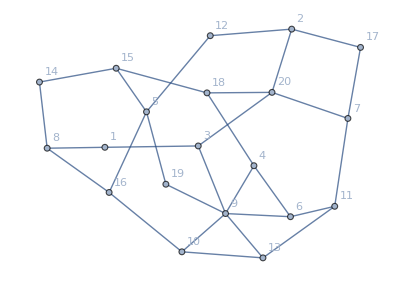

```mathematica
G=Graph[{1<->3,1<->8,2<->20,2<->17,2<->12,3<->9,3<->20,4<->6,4<->9,4<->18,5<->12,5<->15, 5<->19,5<->16,6<->9, 6<->11,7<->11,7<->20, 7<->17,8<->16,8<->14,9<->10,9<->13,9<->19,10<->13,10<->16,11<->13,14<->15,15<->18, 18<->20}, VertexLabels->Automatic]
```

Задание 2. Построить матрицу.

```mathematica
MatrixForm[AdjacencyMatrix[G]]
```

(0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0)

```mathematica
MatrixForm[IncidenceMatrix[G],TableHeadings->{Range[1,20],{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5],Subscript[a, 6],Subscript[a, 7],Subscript[a, 8],Subscript[a, 9],Subscript[a, 10],Subscript[a, 11],Subscript[a, 12],Subscript[a, 13],Subscript[a, 14],Subscript[a, 15],Subscript[a, 16],Subscript[a, 17],Subscript[a, 18],Subscript[a, 19],Subscript[a, 20],Subscript[a, 21],Subscript[a, 22],Subscript[a, 23],Subscript[a, 24],Subscript[a, 25],Subscript[a, 26],Subscript[a, 27],Subscript[a, 28],Subscript[a, 29],Subscript[a, 30]}}]
```

( | a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | a_7 | a_8 | a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | a_15 | a_16 | a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | a_23 | a_24 | a_25 | a_26 | a_27 | a_28 | a_29 | a_30
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
6 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0)

Задание 3.  Составить обход графа и построить деревья обхода

```mathematica
width=BreadthFirstScan[G,W]
```

{3,9,1,20,18,7,5,4,4,4,4,19,18,9,10,6,11,15,9,9}

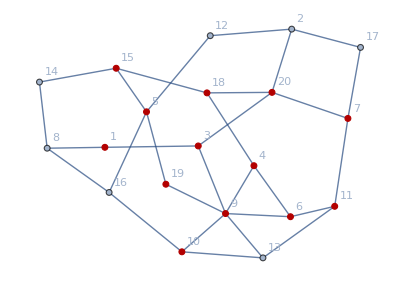

```mathematica
HighlightGraph[G, %]
```

```mathematica
length=DepthFirstScan[G,W]
```

{3,9,1,12,2,7,5,6,4,4,20,16,18,5,8,7,20,15,13,11}

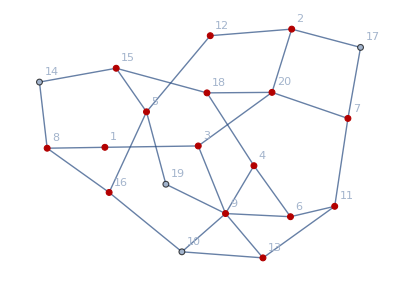

```mathematica
HighlightGraph[G,%]
```

Задание 4.  Матрица расстояний

```mathematica
GraphDistanceMatrix[G]
```

{{0,1,1,3,2,4,4,2,3,3,3,3,3,3,2,4,3,2,3,3},{1,0,2,2,1,3,3,1,2,2,2,3,3,2,3,3,2,3,2,2},{1,2,0,4,3,5,3,3,4,4,3,2,2,3,1,4,4,1,2,3},{3,2,4,0,1,1,1,3,3,4,2,2,3,3,3,3,2,4,4,4},{2,1,3,1,0,2,2,2,2,3,1,3,2,3,4,2,1,3,3,3},{4,3,5,1,2,0,2,4,4,3,3,3,4,4,4,2,1,5,4,3},{4,3,3,1,2,2,0,3,4,4,3,1,2,2,2,4,3,3,3,4},{2,1,3,3,2,4,3,0,1,1,2,2,3,1,2,2,3,4,1,1},{3,2,4,3,2,4,4,1,0,1,1,3,2,2,3,2,3,3,2,2},{3,2,4,4,3,3,4,1,1,0,2,3,3,2,3,1,2,4,2,2},{3,2,3,2,1,3,3,2,1,2,0,2,1,3,3,3,2,2,3,3},{3,3,2,2,3,3,1,2,3,3,2,0,1,1,1,4,4,2,2,3},{3,3,2,3,2,4,2,3,2,3,1,1,0,2,2,4,3,1,3,4},{3,2,3,3,3,4,2,1,2,2,3,1,2,0,2,3,4,3,2,2},{2,3,1,3,4,4,2,2,3,3,3,1,2,2,0,3,4,2,1,2},{4,3,4,3,2,2,4,2,2,1,3,4,4,3,3,0,1,5,2,1},{3,2,4,2,1,1,3,3,3,2,2,4,3,4,4,1,0,4,3,2},{2,3,1,4,3,5,3,4,3,4,2,2,1,3,2,5,4,0,3,4},{3,2,2,4,3,4,3,1,2,2,3,2,3,2,1,2,3,3,0,1},{3,2,3,4,3,3,4,1,2,2,3,3,4,2,2,1,2,4,1,0}}

Задание 5.  Диаметр, радиус, центр графа

```mathematica
GraphCenter[G]
```

{3,18}

```mathematica
GraphRadius[G]
```

3

```mathematica
GraphDiameter[G]
```

5

Задание 6.  Простой цикл.

```mathematica
m=0;
For[i=0,i<Infinity,i++,
If[Length[FindCycle[{G,W},{i,Infinity}]]≠0,If[Length[Part[FindCycle[{G,W},{i,Infinity}],1]]≠0,m=Length[Part[FindCycle[{G,W},{i,Infinity}],1]],Break[]],Break[]]]
C1=FindCycle[{G,11},{m,Infinity}]
```

{{11<->6,6<->4,4<->18,18<->15,15<->14,14<->8,8<->1,1<->3,3<->20,20<->7,7<->17,17<->2,2<->12,12<->5,5<->16,16<->10,10<->9,9<->13,13<->11}}

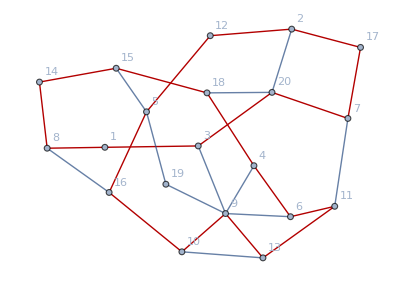

```mathematica
HighlightGraph[G,C1]
```